```mathematica
(* Lets solve the Friedman equation in several cases *)

(* parameter k, ( k=1 for sphere, k=0 for flat ) *)

(* parameter Lambda, cosmological constant or dark energy *)

(* parameter m, matter energy density m/a^3 *)

(* parameter C, radiation energy density C/a^4 *)

(* Goal is to solve Friedmann's equation for a(t) the radius of the Universe at time t *)


(* First case k=1, Lambda=3, we will use units 8 pi G = 1 and speed of light =1 *)
```

```mathematica
(* First step is to solve for t as an integral over a ( I use x here for a *)
```

```mathematica
∫((Λ x^2)/3-k )^(-1/2)ⅆx
```

(√3 ArcTanh[(x √Λ)/(√(-3 k+x^2 Λ))])/(√Λ)

```mathematica
(* this give t as a function of a, but what we want is a as a function of t a(t) *)

(* We can use Solve to invert this and obtain a(t)*)

Solve[t==(√3 ArcTanh[(x √Λ)/(√(-3 k+x^2 Λ))])/(√Λ),x]
```

{{x→-(√3 √k Tanh[(t √Λ)/(√3)])/(√(-Λ+Λ Tanh[(t √Λ)/(√3)]^2))},{x→(√3 √k Tanh[(t √Λ)/(√3)])/(√(-Λ+Λ Tanh[(t √Λ)/(√3)]^2))}}

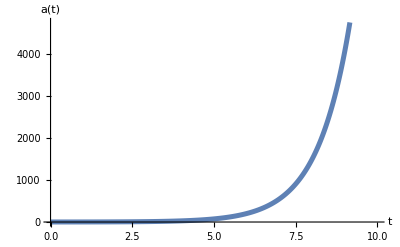

```mathematica
(* This gives a(t) but the form is too complicated. It turns out to be just Cosh[t sqrt(Lambda/3)]*)

(* Lets Plot a(t) for Lambda = 3 to check this *)

Plot[{Cosh[t],(√3 √1 Tanh[(t √3)/(√3)])/(√(-3+3 Tanh[(t √3)/(√3)]^2))},{t,0,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

```mathematica
(* In either form a(t) increases expontentiall at large times, the Universe is accelerating *)

(* Note this may happen at early times as well if inflation is correct *)




(* Radiation and Lambda  : As a second case lets study k=0 spatially flat, m=0. C=1 and Lambda =.1 *)
```

```mathematica
(* Again first step is to solve for t as an integral (again I use x for a *)

∫(Λ/3 x^2+1/x^2)^(-1/2)ⅆx
```

```mathematica
(√(3+x^4 Λ) ArcSinh[(x^2 √Λ)/(√3)])/(2 x √Λ √(1/x^2+(x^2 Λ)/3))
(* This gives t(a) but we use Sove to obtain a(t) *)

Solve[t==(√(3+x^4 Λ) ArcSinh[(x^2 √Λ)/(√3)])/(2 x √Λ √(1/x^2+(x^2 Λ)/3)),x]
```

(√(3+x^4 Λ) ArcSinh[(x^2 √Λ)/(√3)])/(2 x √Λ √(1/x^2+(x^2 Λ)/3))

{{x→-(3^(1/4) √Sinh[(2 t √Λ)/(√3)])/Λ^(1/4)},{x→(3^(1/4) √Sinh[(2 t √Λ)/(√3)])/Λ^(1/4)}}

```mathematica
(* This gives a(t) now Plot the result *)
```

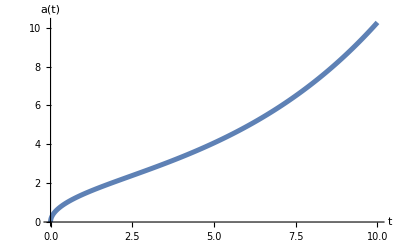

```mathematica
Plot[(3^(1/4) √Sinh[(2 t √(.1))/(√3)])/(.1)^(1/4),{t,0,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

```mathematica
(* Here a(t) goes like t^{1/2} at small t and exponentially for large t *)
```

```mathematica
(* Final example is matter plus Lambda *)

(* Here k=0 spatially flat m=1 , C=0 and Lambda = .1 *)

(* Again solve for t as a integral over a which we denote as x *)

∫(Λ/3 x^2+1/x)^(-1/2)ⅆx
```

(2 √(3+x^3 Λ) ArcSinh[(x^(3/2) √Λ)/(√3)])/(3 √x √Λ √(1/x+(x^2 Λ)/3))

```mathematica
(* Use Solve to invert this to find a(t) *)


Solve[t==(2 √(3+x^3 Λ) ArcSinh[(x^(3/2) √Λ)/(√3)])/(3 √x √Λ √(1/x+(x^2 Λ)/3)),x]
```

{{x→-((-3)^(1/3) Sinh[1/2 √3 t √Λ]^(2/3))/Λ^(1/3)},{x→(3^(1/3) Sinh[1/2 √3 t √Λ]^(2/3))/Λ^(1/3)},{x→((-1)^(2/3) 3^(1/3) Sinh[1/2 √3 t √Λ]^(2/3))/Λ^(1/3)}}

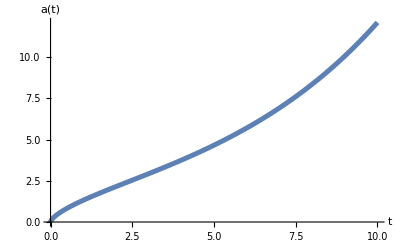

```mathematica
(* Now plot the solution a(t) *)

Plot[(3^(1/3) Sinh[1/2 √3 t √(.1)]^(2/3))/(.1)^(1/3),{t,0,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

```mathematica
(* For matter plus Lambda the Universe expands as t^{2/3} at early times and expontentially for late times *)

(* Next steps are to put realistic values for k, m, C and Lambda, and plot a(t) *)

(* we can also derive a ficticious potential that can give rise to the trajectory a(t) as a solution *)
```